```mathematica
PRAVOKOTNIK,KVADER, KVADRAT, KOCKA
```

```mathematica
*PRAVOKOTNIK IN KVADER
```

Pravokotnik je osno somere in središčno someren lik. Je štirikotnik, kjer sta sosednji dve stranici med seboj pravokotni. Nasprotni stranici sta enako dolgi in vzporedni. Daljici, ki vežeta nasprotni ogljišči imenujemo diagonali, ki ju označimo z e in f. Doagonali se med seboj razpolavljata. Vsi koti v pravokotniku so pravi koti. Višina na stranico a je enaka stranici b in višina na stranico b je enaka stranici a.

```mathematica
Obseg pravokotnika: 2a+2b
Ploščina pravokotnika: a*b
```

Obseg lika je dolžina sklenjene črte, ki omejuje lik. Izračunamo ga z merskim številom in dolžinsko enoto. 
Ploščina lika je enaka velikosti ploskve lika. Izračunamo jo z merskim številom in pliščinsko enoto.

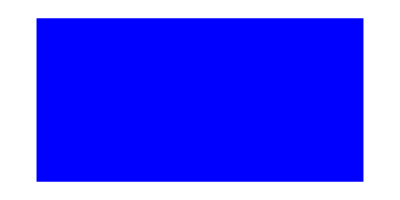

```mathematica
Graphics[{Blue,Rectangle[{2,1},{4,2}]}]
```

Kvader je oglato geometrijsko telo, ki ga omejuje šest mejnih ploskev. Po dve in dve mejni ploskvi sta skladni in vzporedni. Kvader ima 12 robov in 8 ogljišč. Dvev ploskvi sta osnovni ploskvi (ploskev na kateri kvader stoji in njej vzporedna ploskva), druge štiri pa tvorijo plašč kvadra. Kvader ima tri skupine s po štiri skladnimi in vzporednimi robovi. Zato kvader določajo trije značilni robovi: dolžina, širina in višina. Navadno jih označimo po vrsti z a, b in c.  Telesna diagonala je daljica, ki povezuje dve ogljišči različnih ploskev, na primer AC, BH, DF, označujemo jo z d in so med seboj skoladne.

```mathematica
Površina kvadra: 2(ab+ac+bc)
Volmen kvadra: a*b*c
```

Površina telesa je vsota ploščin nejnih ploskev. Kvader ima 2 osnovni ploskvi, ostale sestavljajo plašč. Če površje kvadra razvijemo  v ravnino, dobimo pravokotnike.
Prostornino kvadra dobimo kot produkt merskih števil dolžine, širine ter višine.

```mathematica
število:=RandomReal[1.,{3}]
kvader:=Polygon[Table[število,{3}]]
Graphics3D[kvader]
```

-Graphics3D-

```mathematica
d=Graphics3D[Line[{{1,1,-1},{4,4,1}}]]
```

-Graphics3D-

```mathematica
Risanje grafov - pravokotniki:
```

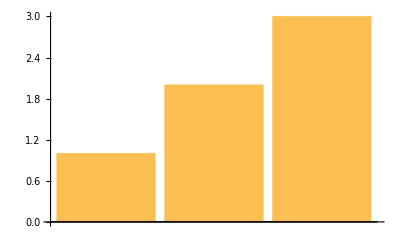

```mathematica
RectangleChart[{{1,1},{1,2},{1,3}}]
```

```mathematica
Zaokroženi pravokotniki:
```

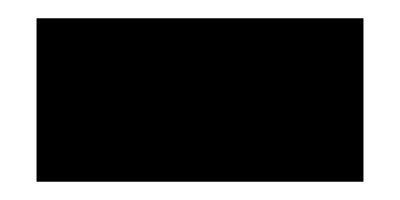

```mathematica
Graphics[Rectangle[{0,0},{2,1},RoundingRadius->0.3]]
```

```mathematica
Framed[1/ROM+y+z,RoundingRadius->10]
```

1/ROM+y+z

```mathematica
3D oblike:
```

```mathematica
Graphics3D[{Yellow,Cuboid[{0,0,0},{1,3,1}],Blue,Cuboid[{2,1,1},{4,2,3}]}]
```

-Graphics3D-

```mathematica
*KVADRAT IN KOCKA
```

Kvadrat je osno someren in sredično somere štirikotnik. Je posebne vrste štirikotnik, saj je pravokoten, ki ima vse stranice enako dolge. Daljici, ki vežeta ogljišči kvadrata imenujemo diagonali, ki ju označujemo v e in f. Diagonali e in f sta enaki in se sekata pravokotno. Vsi koti v kvadratu so pravi koti.

```mathematica
Obseg kvadrata: 4*a
```

```mathematica
Ploščina kvadrata: a^2
```

Obseg lika je dolžina sklenjene črte, ki omejuje lik. Obsek je enak štikratni vsoti ene stranice. 
Ploščina lika je enaka velikosti ploskve lika. Enaka je produktu sosednjih stranic.



```mathematica
Graphics[Rectangle[]]
```

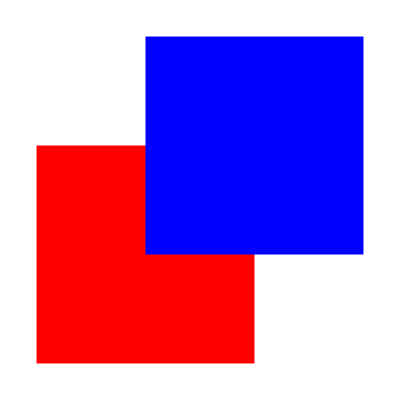

```mathematica
Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]
```

Kocka je oglato geometrijsko telo, ki ga omejuje šest skladnih ploskev, ki imajo obliko kvadrata. Kocka ima 12 robov in 8 ogljišč. Dve izbrani ploskvi sta osnovni, ostale štiri pa tvorijo plačš kocke. Kocka je enakorobi kvader.

```mathematica
Površina kocke:6*a^2
Prostornina kocke: a^3
```

Površina telesa je vsota ploščin vseh mejnih ploskev. Kocka ima 2 osnovni ploskvi in plašč. Če kocko razvijemo dobimo kvadrate.
Prostornino izračunamo podobno kot pri kvadru, le da so vsi robovi enaki a = b = c.

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

```mathematica
Graphics3D[{Yellow,Cuboid[{0,0,0}],Blue,Cuboid[{0.5,0.5,0.5}]}]
```

-Graphics3D-